```mathematica
ClearAll["Global`*"]
```

```mathematica
<<"/Users/alexdeich/thesis/code/mine/ThesisTools.m"
```

```mathematica
?ThesisTools`*
```

## Setting up the Lagrangian

```mathematica
Xd = D[{t[tau],r[tau],T[tau],P[tau]},tau];
```

```mathematica
Ll = Xd.GetKerrgll[M,a,r[tau], T[tau]].Xd
```

((a^2 Cos[T[tau]]^2+r[tau]^2) r'[tau]^2)/(a^2-2 M r[tau]+r[tau]^2)+t'[tau] (-(2 a M r[tau] Sin[T[tau]]^2 P'[tau])/(a^2 Cos[T[tau]]^2+r[tau]^2)+(-1+(2 M r[tau])/(a^2 Cos[T[tau]]^2+r[tau]^2)) t'[tau])+P'[tau] ((Sin[T[tau]]^2 ((a^2+r[tau]^2)^2-a^2 (a^2-2 M r[tau]+r[tau]^2) Sin[T[tau]]^2) P'[tau])/(a^2 Cos[T[tau]]^2+r[tau]^2)-(2 a M r[tau] Sin[T[tau]]^2 t'[tau])/(a^2 Cos[T[tau]]^2+r[tau]^2))+(a^2 Cos[T[tau]]^2+r[tau]^2) T'[tau]^2

```mathematica
tpreps = Simplify[Solve[{D[Ll,t'[tau]] == -Ee, D[Ll,P'[tau]] == Jz},{t'[tau],P'[tau]}]]
```

{{t'[tau]→(2 a^4 Ee Cos[T[tau]]^2-2 a M (-a Ee+2 Jz+a Ee Cos[2 T[tau]]) r[tau]+a^2 Ee (3+Cos[2 T[tau]]) r[tau]^2+2 Ee r[tau]^4)/(4 (a^2 Cos[T[tau]]^2+r[tau]^2) (a^2-2 M r[tau]+r[tau]^2)),P'[tau]→(Csc[T[tau]]^2 (a^2 Jz Cos[T[tau]]^2-M (-a Ee+2 Jz+a Ee Cos[2 T[tau]]) r[tau]+Jz r[tau]^2))/(2 (a^2 Cos[T[tau]]^2+r[tau]^2) (a^2-2 M r[tau]+r[tau]^2))}}

```mathematica
Ll = Simplify[Ll /. tpreps[[1]] /. T'[tau] -> 0 /. T[tau] -> Pi/2]
```

(-2 (-a Ee+Jz)^2 M+(-a^2 Ee^2+Jz^2) r[tau]-r[tau]^3 (Ee^2-4 r'[tau]^2))/(4 r[tau] (a^2-2 M r[tau]+r[tau]^2))

```mathematica
Pprime = (Csc[T[tau]]^2 (a^2 Jz Cos[T[tau]]^2-M (-a Ee+2 Jz+a Ee Cos[2 T[tau]]) r[tau]+Jz r[tau]^2))/(2 (a^2 Cos[T[tau]]^2+r[tau]^2) (a^2-2 M r[tau]+r[tau]^2)) /. T[tau] -> Pi/2
```

(-(-2 a Ee+2 Jz) M r[tau]+Jz r[tau]^2)/(2 r[tau]^2 (a^2-2 M r[tau]+r[tau]^2))

```mathematica
tprime = (2 a^4 Ee Cos[T[tau]]^2-2 a M (-a Ee+2 Jz+a Ee Cos[2 T[tau]]) r[tau]+a^2 Ee (3+Cos[2 T[tau]]) r[tau]^2+2 Ee r[tau]^4)/(4 (a^2 Cos[T[tau]]^2+r[tau]^2) (a^2-2 M r[tau]+r[tau]^2))/.T[tau]-> Pi/2
```

(-2 a (-2 a Ee+2 Jz) M r[tau]+2 a^2 Ee r[tau]^2+2 Ee r[tau]^4)/(4 r[tau]^2 (a^2-2 M r[tau]+r[tau]^2))

```mathematica
r2 = r'[tau]^2 //. Solve[Ll == -1,r'[tau]][[1]]
```

1/r[tau]^2(a^2-2 M r[tau]+r[tau]^2) (-1+(a^2 Ee^2)/(4 (a^2-2 M r[tau]+r[tau]^2))-Jz^2/(4 (a^2-2 M r[tau]+r[tau]^2))+(a^2 Ee^2 M)/(2 r[tau] (a^2-2 M r[tau]+r[tau]^2))-(a Ee Jz M)/(r[tau] (a^2-2 M r[tau]+r[tau]^2))+(Jz^2 M)/(2 r[tau] (a^2-2 M r[tau]+r[tau]^2))+(Ee^2 r[tau]^2)/(4 (a^2-2 M r[tau]+r[tau]^2)))

```mathematica
rpp =Simplify[Expand[ D[r2,tau]/(2 r'[tau])]]
```

(-3 (-a Ee+Jz)^2 M+(-a^2 (-4+Ee^2)+Jz^2) r[tau]-4 M r[tau]^2)/(4 r[tau]^4)

```mathematica
(-3 (-a Ee+Jz)^2 M+(-a^2 (-4+Ee^2)+Jz^2) r[tau]-4 M r[tau]^2)/(4 r[tau]^4)
```

(-3 (-a Ee+Jz)^2 M+(-a^2 (-4+Ee^2)+Jz^2) r[tau]-4 M r[tau]^2)/(4 r[tau]^4)

```mathematica
Simplify[Solve[-3 (-a Ee+Jz)^2 M+(-a^2 (-4+Ee^2)+Jz^2) r[tau]-4 M r[tau]^2 ==0,r[tau]]]
```

{{r[tau]→(4 a^2-a^2 Ee^2+Jz^2-√((-a^2 (-4+Ee^2)+Jz^2)^2-48 (-a Ee+Jz)^2 M^2))/(8 M)},{r[tau]→(4 a^2-a^2 Ee^2+Jz^2+√((-a^2 (-4+Ee^2)+Jz^2)^2-48 (-a Ee+Jz)^2 M^2))/(8 M)}}

## Full Integrator- one particle Here, the RK4 integrator takes a x with {t,r,rdot,phi}

```mathematica
G[x_,f_] := {f[[2]], (-3 (-a[x] Ee+Jz)^2 M+(-a[x]^2 (-4+Ee^2)+Jz^2) f[[1]]-4 M f[[1]]^2)/(4 f[[1]]^4),(-(-2 a[x] Ee+2 Jz) M f[[1]]+Jz f[[1]]^2)/(2 f[[1]]^2 (a[x]^2-2 M f[[1]]+f[[1]]^2))}
```

two different spin functions

```mathematica
a[x_] := If[x  ≤ 10000, 0., .99]
```

```mathematica
a[x_] :=0.
```

Getting an initial stable orbit for some total energy and jz.

```mathematica
M = 1.;
Ee = 5.;
Jz = 7.;
Rinit = (4 a[0]^2-a[0]^2 Ee^2+Jz^2+√((-a[0]^2 (-4+Ee^2)+Jz^2)^2-48 (-a[0] Ee+Jz)^2 M^2))/(8 M)
```

7.

```mathematica
fnvals = RKODE4[G, 0., {Rinit+0.5, 0., 0.},.01,20000];
```

```mathematica
xyplot = Table[{fnvals[[j,2,1]] Cos[fnvals[[j,2,3]]], fnvals[[j,2,1]] Sin[fnvals[[j,2,3]]]},{j,1,Length[fnvals]}];
```

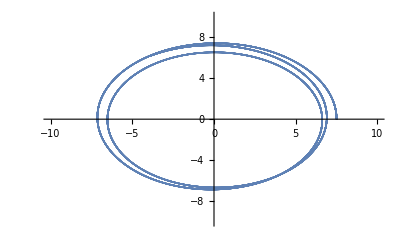

```mathematica
ListPlot[xyplot,PlotRange->{{-10,10},{-10,10}}]
```

## Many particles

Make a bunch of random initial vectors and feed them into the integrator

```mathematica
Nparticles= 1000;
EnergyandMomenta = RandomReal[{1,10},{2,Nparticles}];
InitRadii = RandomReal[{-3,3},{Nparticles}];
InitPhi = RandomReal[{0,2 Pi},{Nparticles}];

ParticleTrajectories = Table[0,Nparticles];
```

```mathematica
InitRadii[[4]]
```

-1.0996

```mathematica
InitRadii
```

{25.9473,30.6689}

```mathematica
EnergyandMomenta[[2,1]]
```

9.17934

#### The big for loop

```mathematica
For[i=1,i≤ Nparticles,i++,
Ee = EnergyandMomenta[[1,i]];
Jz = EnergyandMomenta[[2,i]];

Rinit0 = (4 a[0]^2-a[0]^2 Ee^2+Jz^2+√((-a[0]^2 (-4+Ee^2)+Jz^2)^2-48 (-a[0] Ee+Jz)^2 M^2))/(8 M);

Phi0 = InitPhi[[i]];

G[x_,f_] := {f[[2]], (-3 (-a[x] Ee+Jz)^2 M+(-a[x]^2 (-4+Ee^2)+Jz^2) f[[1]]-4 M f[[1]]^2)/(4 f[[1]]^4),(-(-2 a[x] Ee+2 Jz) M f[[1]]+Jz f[[1]]^2)/(2 f[[1]]^2 (a[x]^2-2 M f[[1]]+f[[1]]^2))};
eom = i;

trajvals = RKODE4[G,0.,{Rinit0+InitRadii[[i]],0.,Phi0},0.001,20000];
trajcheck = i;
xyvals =Table[{trajvals[[j,2,1]] Cos[trajvals[[j,2,3]]], trajvals[[j,2,1]] Sin[trajvals[[j,2,3]]]},{j,1,Length[trajvals]}];

xycheck  =i;
Export["/Users/alexdeich/thesis/code/mine/particle_trajectory_data/1123_2/particle_trajectory_"<>ToString[i]<>".csv",xyvals,"CSV"]
writecheck = i;
]
```

Set::write: Tag Times in 1000\ "/Users/alexdeich/thesis/code/mine/particle_trajectory_data/1123_2/particle_trajectory_1.csv" is Protected.

Set::write: Tag Times in 1000\ "/Users/alexdeich/thesis/code/mine/particle_trajectory_data/1123_2/particle_trajectory_2.csv" is Protected.

Set::write: Tag Times in 1000\ "/Users/alexdeich/thesis/code/mine/particle_trajectory_data/1123_2/particle_trajectory_3.csv" is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

```mathematica
Dynamic["Equation of motion: particle "<>ToString[eom]]
Dynamic["Trajectory calculated: particle "<>ToString[trajcheck]]
Dynamic["XY coordinates calculated: particle "<>ToString[xycheck]]
Dynamic["Written to ParticleTrajectories: particle "<>ToString[writecheck]]
```

```mathematica
Do[Export["/Users/alexdeich/thesis/code/mine/particle_trajectory_data/1123_3/particle_trajectory_"<>ToString[i]<>".csv",ParticleTrajectories[[i]],"CSV"],{i,1,Nparticles}]
```

OpenWrite::noopen: Cannot open "/Users/alexdeich/thesis/code/mine/particle_trajectory_data/1123_3/particle_trajectory_1.csv".

OpenWrite::noopen: Cannot open "/Users/alexdeich/thesis/code/mine/particle_trajectory_data/1123_3/particle_trajectory_2.csv".

OpenWrite::noopen: Cannot open "/Users/alexdeich/thesis/code/mine/particle_trajectory_data/1123_3/particle_trajectory_3.csv".

General::stop: Further output of OpenWrite :: noopen will be suppressed during this calculation.